### La Parábola

```mathematica
f[z_]=(1+ z+2 z^2)/(1+3 z); NSolve[f[z]==-1/3,z]
```

{{z→-0.5-0.645497 ⅈ},{z→-0.5+0.645497 ⅈ}}

```mathematica
NSolve[f[f[z]]==-1/3,z]
```

{{z→-0.80352-1.27508 ⅈ},{z→-0.80352+1.27508 ⅈ},{z→-0.44648-0.306838 ⅈ},{z→-0.44648+0.306838 ⅈ}}

```mathematica
NSolve[f[f[f[z]]]==-1/3,z]
```

{{z→-1.2913-2.08844 ⅈ},{z→-1.2913+2.08844 ⅈ},{z→-0.671952-0.894751 ⅈ},{z→-0.671952+0.894751 ⅈ},{z→-0.497768-0.434494 ⅈ},{z→-0.497768+0.434494 ⅈ},{z→-0.413981-0.175818 ⅈ},{z→-0.413981+0.175818 ⅈ}}

```mathematica
NSolve[f[f[f[f[z]]]]==-1/3.,z]
```

{{z→-2.04692-3.23986 ⅈ},{z→-2.04692+3.23986 ⅈ},{z→-1.06653-1.57413 ⅈ},{z→-1.06653+1.57413 ⅈ},{z→-0.759026-1.02226 ⅈ},{z→-0.759026+1.02226 ⅈ},{z→-0.607128-0.774055 ⅈ},{z→-0.607128+0.774055 ⅈ},{z→-0.513844-0.510328 ⅈ},{z→-0.513844+0.510328 ⅈ},{z→-0.487625-0.370517 ⅈ},{z→-0.487625+0.370517 ⅈ},{z→-0.441398-0.232008 ⅈ},{z→-0.441398+0.232008 ⅈ},{z→-0.390029-0.107193 ⅈ},{z→-0.390029+0.107193 ⅈ}}

```mathematica
datos={{-1/3,0},{-0.5,0.6454972243679027},{-0.8035201808187874,-1.2750840140066675}, {-0.8035201808187874,1.2750840140066675},{-1.2912993557438488,2.0884443522737923}, {-2.046920333167267,3.239860238742131}}
```

{{-1/3,0},{-0.5,0.645497},{-0.80352,-1.27508},{-0.80352,1.27508},{-1.2913,2.08844},{-2.04692,3.23986}}

```mathematica
recta = Fit[datos, {1,x}, x]
```

-0.935106-2.00472 x

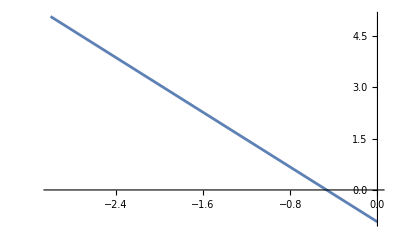

```mathematica
Plot[recta,{x,-3,0}]
```

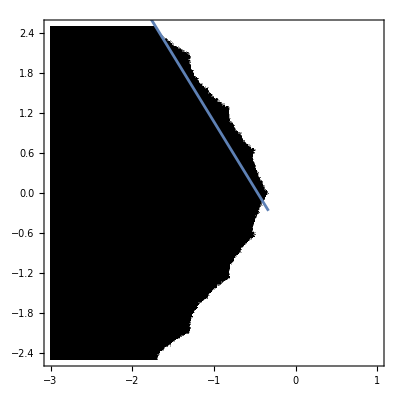

```mathematica
m=2;iter2=Compile[{{z,_Complex}},(1+(-1+m) z+m z^2)/(-1+m+z+m z)];aproxpfijo=Compile[{{z,_Complex}}, Which[Abs[z-1]<10.0^(-6), 2,
Abs[z+1]<10.0^(-6), 1,
True, 0]];
iterAlgorithm[iterMethod_, x_, y_, lim_]:=
Block[{z,ct,r}, z=x+I*y;ct=0; r=aproxpfijo[z]; 
While[(r==0) && (ct < lim),
	++ct; z=iterMethod[z]; r=aproxpfijo[z]];
If[Head[r]==Which, r=0]; (*"Which" unevaluated *)
Return[r]];
limIterations=50; xxMin=-3; xxMax=1; yyMin=-2.5;yyMax=2.5;
plotFractal[iterMethod_,points_]:= DensityPlot[iterAlgorithm[iterMethod,x, y, limIterations],{x,xxMin, xxMax}, {y,yyMin,yyMax}, PlotRange->{0,2}, PlotPoints->points, Mesh->False,ColorFunction->GrayLevel
]//Timing;
dibu2=plotFractal[iter2, 128];dibu1=Plot[recta,{x,-3,-1/3}];Show[ dibu2[[2]],dibu1]
```